```mathematica
Unprotect[$Notebooks];
$Notebooks=True;
<<"PlotGrid`";
```

```mathematica
<<"cmdline`opt`";
<<"cmdline`log`";
<<"filestruct`";
<<"QSF`";
<<"QSF`wf`";
```

Needs::nocont: Context QSF`wf`styling` was not created when Needs was evaluated.

{QSF`wf`,cmdline`log`,cmdline`opt`,QSF`wf`styling`,PlotGrid`,QSF`ColorFunctions`,System`}

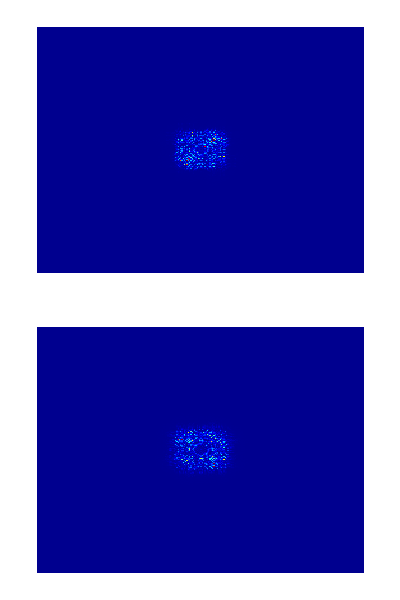

```mathematica
WFGrid[{{WFPlot@AbsSquare@WFLoad["/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/model_es/flux_quiver_ratio_2.000000/nm_775/fwhm_cycles_13.540000/phase_0.500000/momenta_repP.psi3"]},{WFPlot@AbsSquare@WFLoad["/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/model_eb/flux_quiver_ratio_2.000000/nm_775/fwhm_cycles_13.540000/phase_0.500000/momenta_repP.psi3"]}},PlotRange->Max]
```

```mathematica
fileStruct=ParsePattern[(*"Results/model_*/flux_quiver_ratio_2.000000/nm_*/fwhm_cycles_**/phase_0.5***/momenta_repP.psi3"];*)"Results/model_*/flux_quiver_ratio_2.000000/nm_7**/fwhm_cycles_3***/phase_0.****/momenta_repP.psi3"];
```

{Users}

{Projects}

{Quantum}

/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/model_eb/flux_quiver_ratio_2.000000/nm_775/fwhm_cycles_3.965000/phase_0.000000/momenta_repP.psi3

/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/model_eb/flux_quiver_ratio_2.000000/nm_775/fwhm_cycles_3.965000/phase_0.250000/momenta_repP.psi3

/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/model_eb/flux_quiver_ratio_2.000000/nm_775/fwhm_cycles_3.965000/phase_0.500000/momenta_repP.psi3

/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/model_es/flux_quiver_ratio_2.000000/nm_775/fwhm_cycles_3.965000/phase_0.000000/momenta_repP.psi3

/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/model_es/flux_quiver_ratio_2.000000/nm_775/fwhm_cycles_3.965000/phase_0.250000/momenta_repP.psi3

/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/model_es/flux_quiver_ratio_2.000000/nm_775/fwhm_cycles_3.965000/phase_0.500000/momenta_repP.psi3

```mathematica
processed=StructProcess[fileStruct,"Operations"->{"TrimMarginsPercent"->0.2,4->TrimMargins@*Average@*RemoveBoundedPart@*WFLoad,StructPeak,{PrettyPlots,"WFExportPath"->"melo",1->WFExport@*WFGrid@*WFPlot@*AbsSquare}
(* ,{"LegendPlacement"->Top,GridLines->Full,Axes->False,PlotRange->{{0,2},Full},"WFExportPath"->"elo",PrettyPlots,3->WFCombine@*GaussianBlur@*TransverseDiagSum@*MergeOrthants,StructPeak,1->WFExport,StructPeak}*)
(*{GridLines->Full,Axes->False,PlotRange->Full,0->WFPlot,StructPeak,WFExport}*)}];
```

```mathematica
PlotGrid2[{{a,b}}]
PlotGrid1[{{a,b}}]
PlotGrid0[{{a,b}}]
```

```mathematica
wfs={{WFPlot@AbsSquare@WFLoad["/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/model_es/flux_quiver_ratio_2.000000/nm_775/fwhm_cycles_13.540000/phase_0.500000/momenta_repP.psi3"]},{WFPlot@AbsSquare@WFLoad["/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/model_eb/flux_quiver_ratio_2.000000/nm_775/fwhm_cycles_13.540000/phase_0.500000/momenta_repP.psi3"]}};
```

```mathematica
PlotGrid0[wfs]
PlotGrid1[wfs]
PlotGrid2[wfs]
```

```mathematica
wf=AbsSquare@WFLoad["/Users/ranza/Projects/Quantum/QSF-examples/examples/argon-2e/Results/model_es/flux_quiver_ratio_2.000000/nm_775/fwhm_cycles_13.540000/phase_0.500000/momenta_repP.psi3"];
```

```mathematica
drng=WFDataRange[Header[wf]];
step=WFDataStep[Header[wf]];
(*res=If[HD["isComplex"],HD["isComplex"]=False;Abs[res]^2,res];*)

{min,max}=MinMax[RemoveLegends[Data[wf]]];
```

```mathematica
im1=ArrayPlot[Reverse@Data[wf],DataReversed->False,FrameTicks->{{True,None},{True,None}},PlotRange->Full,PlotRangePadding->0,ImageSize->405,ColorFunction->Jet,DataRange->WFDataRange[Header[wf]]];
gi=GraphicsInformation[im1]
```

<|ImagePadding→{{17.,1.5},{17.,0.5}},ImageSize→{405.,404.},PlotRangeSize→{386.5,386.5},PlotRange→{{-6.30773,6.25864},{-6.30773,6.25864}}|>

```mathematica
AbsoluteOptionsV:=#2/. AbsoluteOptions[#1,#2]&;
```

```mathematica
BarLegendMantisas:=#/. {NumberForm[y_,{w_,z_}]:>NumberForm[y,0,NumberPoint->"",NumberFormat->(#1&),ExponentFunction->(#&)]}&;
BarLegendExponent:=First[Cases[#,exp_NumberForm:>exp,∞]/. {NumberForm[y_,{w_,z_}]:>NumberForm[y,NumberFormat->(#3&),ExponentFunction->(#&)]}]&;


BarLegendExponentRowText:=Inset[Style[DisplayForm@SuperscriptBox["×10",BarLegendExponent[#]],FontFamily->"Latin Modern Math",FontSize->12 ],{Right,Bottom},{Right,Bottom},Background->White]&;
BarLegendRowExponentNotion:=BarLegendMantisas[Print[FullForm@#];(#/.{Rule[PlotRangePadding,_]->Rule[PlotRangePadding,gi1[ImagePadding]]}/.{Graphics[ccc___]->Graphics[ccc,Epilog->BarLegendExponentRowText[#] ]})]&;

BarLegendExponentColumnText:=Inset[Style[DisplayForm@SuperscriptBox["×10",BarLegendExponent[#]],FontFamily->"Latin Modern Math",FontSize->12],{Right,Top},{Right,Top},Background->White]&;
BarLegendColumnExponentNotion:=BarLegendMantisas[(#/.{Graphics[ccc___]->Graphics[ccc,Epilog->BarLegendExponentColumnText[#]] })]&;
```

```mathematica
RowBarLegended[gr_Graphics,colorFn_, minmax_List]:=Legended[gr,
Placed[
BarLegend[{colorFn,minmax},
LegendLayout->"Row",
LegendFunction->BarLegendRowExponentNotion,
LegendMarkerSize->{1.04,0.04}AbsoluteOptionsV[gr,ImageSize](*-{1.0,0}First@AbsoluteOptionsV[gr,ImagePadding]*),
LegendMargins->{{0,0},{0,0}},
LabelStyle->{Black,FontFamily->"Latin Modern Math",FontSize->12}],
Bottom]
];
ColumnBarLegended[gr_Graphics,colorFn_, minmax_List]:=Legended[gr,
Placed[
BarLegend[{colorFn,minmax},
LegendLayout->"Column",
LegendFunction->BarLegendColumnExponentNotion,
LegendMarkerSize->{0.04,1.04}AbsoluteOptionsV[gr,ImageSize]-{0,1.0}Last@AbsoluteOptionsV[gr,ImagePadding],
LegendMargins->{{0,0},Last@AbsoluteOptionsV[gr,ImagePadding]},
LabelStyle->{Black,FontFamily->"Latin Modern Math",FontSize->12}],
Right]
];
```

```mathematica
im1=ArrayPlot[Reverse@Data[wf],DataReversed->False,FrameTicks->{{True,None},{True,None}},PlotRange->Full,PlotRangePadding->0.1,ImageSize->335,ColorFunction->"Jet",DataRange->WFDataRange[Header[wf]],FrameLabel->{{"bottom","top"},{"left","right"}}];
(*FrameLabel behaves diff than described*)
im2=ArrayPlot[Reverse@Data[wf],DataReversed->False,FrameTicks->{{True,None},{True,None}},PlotRange->Full,PlotRangePadding->None,ImageSize->335,ColorFunction->"Jet",DataRange->WFDataRange[Header[wf]],FrameLabel->{"bottom","top"}];
gi1=GraphicsInformation[im1]
gi2=GraphicsInformation[im2]
```

<|ImagePadding→{{36.,20.},{36.,19.}},ImageSize→{335.,334.},PlotRangeSize→{279.,279.},PlotRange→{{-6.40773,6.35864},{-6.40773,6.35864}}|>

<|ImagePadding→{{36.,1.5},{36.,0.5}},ImageSize→{335.,334.},PlotRangeSize→{297.5,297.5},PlotRange→{{-6.30773,6.25864},{-6.30773,6.25864}}|>

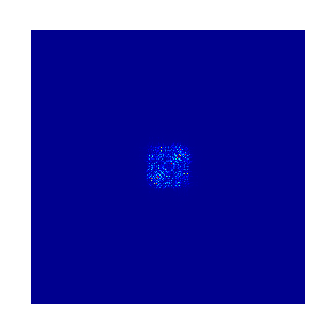
{-Graphics-,-Graphics-}

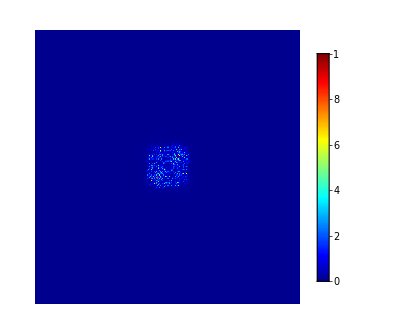
{-Graphics-,-Graphics-}

```mathematica
{RowBarLegended[im1,"Jet",{10^-8,10^-2}],RowBarLegended[im2,"Jet",{10^-8,10^-2}]}
{ColumnBarLegended[im1,"Jet",{10^-8,10^-2}],ColumnBarLegended[im2,"Jet",{10^-8,10^-2}]}
```